# Tarea de interpolación polinomial

## Generación de 20 puntos

```mathematica
a = 1; b = 20;
datos = Table[{x,Sin[x]},{x,a,b,1}]
```

{{1,Sin[1]},{2,Sin[2]},{3,Sin[3]},{4,Sin[4]},{5,Sin[5]},{6,Sin[6]},{7,Sin[7]},{8,Sin[8]},{9,Sin[9]},{10,Sin[10]},{11,Sin[11]},{12,Sin[12]},{13,Sin[13]},{14,Sin[14]},{15,Sin[15]},{16,Sin[16]},{17,Sin[17]},{18,Sin[18]},{19,Sin[19]},{20,Sin[20]}}

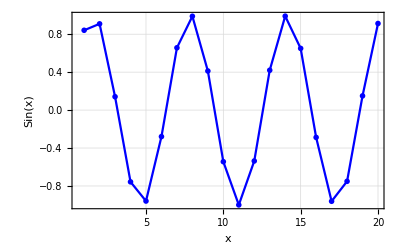

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
]
```

## Ajuste

```mathematica
VandermondeMatrix[xList_]:=Quiet[Table[x^j /.Indeterminate->1,{x,xList},{j,0,Length[xList]-1}]];
PolynomialBase[n_]:=Table[x^j,{j,0,n-1}];
```

```mathematica
MatrixForm@VandermondeMatrix[datos[[All,1]]]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536 | 131072 | 262144 | 524288
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721 | 129140163 | 387420489 | 1162261467
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296 | 17179869184 | 68719476736 | 274877906944
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625 | 762939453125 | 3814697265625 | 19073486328125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456 | 16926659444736 | 101559956668416 | 609359740010496
1 | 7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601 | 232630513987207 | 1628413597910449 | 11398895185373143
1 | 8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656 | 2251799813685248 | 18014398509481984 | 144115188075855872
1 | 9 | 81 | 729 | 6561 | 59049 | 531441 | 4782969 | 43046721 | 387420489 | 3486784401 | 31381059609 | 282429536481 | 2541865828329 | 22876792454961 | 205891132094649 | 1853020188851841 | 16677181699666569 | 150094635296999121 | 1350851717672992089
1 | 10 | 100 | 1000 | 10000 | 100000 | 1000000 | 10000000 | 100000000 | 1000000000 | 10000000000 | 100000000000 | 1000000000000 | 10000000000000 | 100000000000000 | 1000000000000000 | 10000000000000000 | 100000000000000000 | 1000000000000000000 | 10000000000000000000
1 | 11 | 121 | 1331 | 14641 | 161051 | 1771561 | 19487171 | 214358881 | 2357947691 | 25937424601 | 285311670611 | 3138428376721 | 34522712143931 | 379749833583241 | 4177248169415651 | 45949729863572161 | 505447028499293771 | 5559917313492231481 | 61159090448414546291
1 | 12 | 144 | 1728 | 20736 | 248832 | 2985984 | 35831808 | 429981696 | 5159780352 | 61917364224 | 743008370688 | 8916100448256 | 106993205379072 | 1283918464548864 | 15407021574586368 | 184884258895036416 | 2218611106740436992 | 26623333280885243904 | 319479999370622926848
1 | 13 | 169 | 2197 | 28561 | 371293 | 4826809 | 62748517 | 815730721 | 10604499373 | 137858491849 | 1792160394037 | 23298085122481 | 302875106592253 | 3937376385699289 | 51185893014090757 | 665416609183179841 | 8650415919381337933 | 112455406951957393129 | 1461920290375446110677
1 | 14 | 196 | 2744 | 38416 | 537824 | 7529536 | 105413504 | 1475789056 | 20661046784 | 289254654976 | 4049565169664 | 56693912375296 | 793714773254144 | 11112006825558016 | 155568095557812224 | 2177953337809371136 | 30491346729331195904 | 426878854210636742656 | 5976303958948914397184
1 | 15 | 225 | 3375 | 50625 | 759375 | 11390625 | 170859375 | 2562890625 | 38443359375 | 576650390625 | 8649755859375 | 129746337890625 | 1946195068359375 | 29192926025390625 | 437893890380859375 | 6568408355712890625 | 98526125335693359375 | 1477891880035400390625 | 22168378200531005859375
1 | 16 | 256 | 4096 | 65536 | 1048576 | 16777216 | 268435456 | 4294967296 | 68719476736 | 1099511627776 | 17592186044416 | 281474976710656 | 4503599627370496 | 72057594037927936 | 1152921504606846976 | 18446744073709551616 | 295147905179352825856 | 4722366482869645213696 | 75557863725914323419136
1 | 17 | 289 | 4913 | 83521 | 1419857 | 24137569 | 410338673 | 6975757441 | 118587876497 | 2015993900449 | 34271896307633 | 582622237229761 | 9904578032905937 | 168377826559400929 | 2862423051509815793 | 48661191875666868481 | 827240261886336764177 | 14063084452067724991009 | 239072435685151324847153
1 | 18 | 324 | 5832 | 104976 | 1889568 | 34012224 | 612220032 | 11019960576 | 198359290368 | 3570467226624 | 64268410079232 | 1156831381426176 | 20822964865671168 | 374813367582081024 | 6746640616477458432 | 121439531096594251776 | 2185911559738696531968 | 39346408075296537575424 | 708235345355337676357632
1 | 19 | 361 | 6859 | 130321 | 2476099 | 47045881 | 893871739 | 16983563041 | 322687697779 | 6131066257801 | 116490258898219 | 2213314919066161 | 42052983462257059 | 799006685782884121 | 15181127029874798299 | 288441413567621167681 | 5480386857784802185939 | 104127350297911241532841 | 1978419655660313589123979
1 | 20 | 400 | 8000 | 160000 | 3200000 | 64000000 | 1280000000 | 25600000000 | 512000000000 | 10240000000000 | 204800000000000 | 4096000000000000 | 81920000000000000 | 1638400000000000000 | 32768000000000000000 | 655360000000000000000 | 13107200000000000000000 | 262144000000000000000000 | 5242880000000000000000000)

```mathematica
aVect= N@Inverse[VandermondeMatrix[datos[[All,1]]]].Transpose[{datos[[All,2]]}]
```

{{0.234768},{0.175316},{1.26052},{-1.29649},{0.671739},{-0.274755},{0.0879721},{-0.0208431},{0.00370481},{-0.000506909},{0.0000532346},{-4.12349×10^-6},{2.14993×10^-7},{-5.5401×10^-9},{-1.30909×10^-10},{1.90371×10^-11},{-8.58514×10^-13},{2.13916×10^-14},{-2.944×10^-16},{1.75939×10^-18}}

```mathematica
aList = First@Transpose[aVect]
```

{0.234768,0.175316,1.26052,-1.29649,0.671739,-0.274755,0.0879721,-0.0208431,0.00370481,-0.000506909,0.0000532346,-4.12349×10^-6,2.14993×10^-7,-5.5401×10^-9,-1.30909×10^-10,1.90371×10^-11,-8.58514×10^-13,2.13916×10^-14,-2.944×10^-16,1.75939×10^-18}

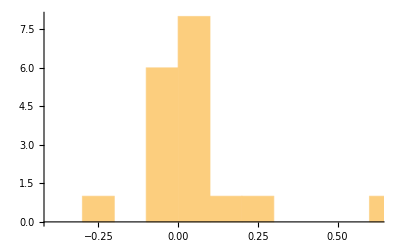

```mathematica
Histogram[aList]
```

```mathematica
PolynomialBase[20]
```

{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15,x^16,x^17,x^18,x^19}

```mathematica
aList.PolynomialBase[20]
```

0.234768+0.175316 x+1.26052 x^2-1.29649 x^3+0.671739 x^4-0.274755 x^5+0.0879721 x^6-0.0208431 x^7+0.00370481 x^8-0.000506909 x^9+0.0000532346 x^10-4.12349×10^-6 x^11+2.14993×10^-7 x^12-5.5401×10^-9 x^13-1.30909×10^-10 x^14+1.90371×10^-11 x^15-8.58514×10^-13 x^16+2.13916×10^-14 x^17-2.944×10^-16 x^18+1.75939×10^-18 x^19

Interpolación

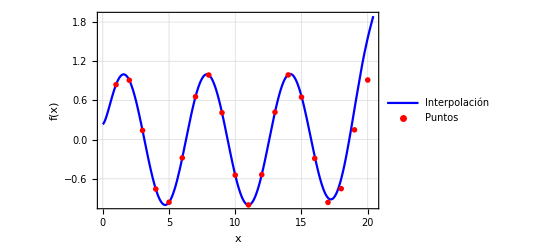

```mathematica
Show[
Plot[
0.23476803377946487+0.17531612254152584 x+1.260519972854416 x^2-1.2964935742738843 x^3+0.6717387330913387 x^4-0.2747545008801662 x^5+0.08797209116436128 x^6-0.02084311578881154 x^7+0.003704810860377189 x^8-0.0005069090667866576 x^9+0.00005323462030153576 x^10-4.123489541991167*^-6 x^11+2.149933248641468*^-7 x^12-5.540100389107323*^-9 x^13-1.309090885587633*^-10 x^14+1.9037139768001322*^-11 x^15-8.585137314851371*^-13 x^16+2.1391626673307167*^-14 x^17-2.944000422242247*^-16 x^18+1.759388204325254*^-18 x^19,
{x,0,6.5π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},PlotLegends->{"Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

Extrapolación

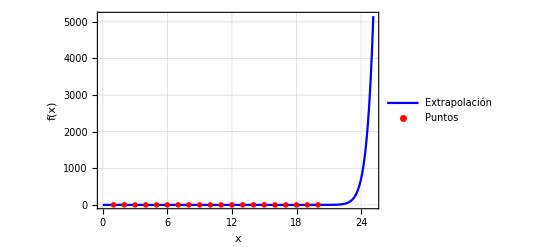

```mathematica
Show[
Plot[
0.23476803377946487+0.17531612254152584 x+1.260519972854416 x^2-1.2964935742738843 x^3+0.6717387330913387 x^4-0.2747545008801662 x^5+0.08797209116436128 x^6-0.02084311578881154 x^7+0.003704810860377189 x^8-0.0005069090667866576 x^9+0.00005323462030153576 x^10-4.123489541991167*^-6 x^11+2.149933248641468*^-7 x^12-5.540100389107323*^-9 x^13-1.309090885587633*^-10 x^14+1.9037139768001322*^-11 x^15-8.585137314851371*^-13 x^16+2.1391626673307167*^-14 x^17-2.944000422242247*^-16 x^18+1.759388204325254*^-18 x^19,
{x,0,8π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},PlotLegends->{"Extrapolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

## Análisis del error

```mathematica
R[x_]:=Sin[x]-(0.23476803377946487+0.17531612254152584 x+1.260519972854416 x^2-1.2964935742738843 x^3+0.6717387330913387 x^4-0.2747545008801662 x^5+0.08797209116436128 x^6-0.02084311578881154 x^7+0.003704810860377189 x^8-0.0005069090667866576 x^9+0.00005323462030153576 x^10-4.123489541991167*^-6 x^11+2.149933248641468*^-7 x^12-5.540100389107323*^-9 x^13-1.309090885587633*^-10 x^14+1.9037139768001322*^-11 x^15-8.585137314851371*^-13 x^16+2.1391626673307167*^-14 x^17-2.944000422242247*^-16 x^18+1.759388204325254*^-18 x^19);
```

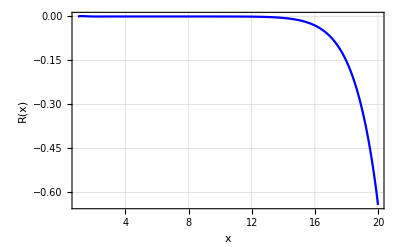

```mathematica
Plot[R[x],{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

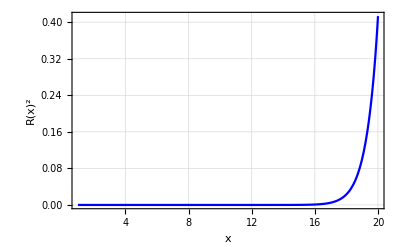

```mathematica
Plot[R[x]^2,{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)^2",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

```mathematica
ϵ = √NIntegrate[R[x]^2,{x,a,b}]
```

0.538936

## El problema de la interpolación polinomial

```mathematica
a = 1; b = 20;
GenerateData[Δ_]:=Table[{x,Sin[x]},{x,a,b,Δ}];
PolynomialInterpolation[data_]:=Block[{aVect,aList},
aVect= Quiet@N@Inverse[VandermondeMatrix[data[[All,1]]]].Transpose[{data[[All,2]]}];
aList = First@Transpose[aVect];

aList.PolynomialBase[Length[aList]]
];
```

```mathematica
datos = GenerateData[0.5]
```

{{1.,0.841471},{1.5,0.997495},{2.,0.909297},{2.5,0.598472},{3.,0.14112},{3.5,-0.350783},{4.,-0.756802},{4.5,-0.97753},{5.,-0.958924},{5.5,-0.70554},{6.,-0.279415},{6.5,0.21512},{7.,0.656987},{7.5,0.938},{8.,0.989358},{8.5,0.798487},{9.,0.412118},{9.5,-0.0751511},{10.,-0.544021},{10.5,-0.879696},{11.,-0.99999},{11.5,-0.875452},{12.,-0.536573},{12.5,-0.0663219},{13.,0.420167},{13.5,0.803784},{14.,0.990607},{14.5,0.934895},{15.,0.650288},{15.5,0.206467},{16.,-0.287903},{16.5,-0.711785},{17.,-0.961397},{17.5,-0.975626},{18.,-0.750987},{18.5,-0.342481},{19.,0.149877},{19.5,0.60554},{20.,0.912945}}

```mathematica
PolynomialInterpolation[datos]
```

-0.00696693+1.02988 x-0.0560377 x^2-0.105866 x^3-0.0423001 x^4+0.0278857 x^5-0.00584119 x^6+0.000709438 x^7+0.000071005 x^8-0.0000806574 x^9+0.0000251356 x^10-4.66229×10^-6 x^11+5.75885×10^-7 x^12-4.65298×10^-8 x^13+1.96268×10^-9 x^14+3.13554×10^-11 x^15-8.9929×10^-12 x^16+3.64148×10^-13 x^17+9.29652×10^-15 x^18-1.08824×10^-15 x^19+7.71627×10^-18 x^20+6.87056×10^-19 x^21+8.30078×10^-20 x^22-3.69348×10^-21 x^23-2.23576×10^-22 x^24+4.12616×10^-24 x^25+9.61179×10^-25 x^26-1.68862×10^-26 x^27-1.75649×10^-27 x^28-4.29013×10^-29 x^29+1.01749×10^-29 x^30-3.46978×10^-31 x^31+5.19635×10^-33 x^32-2.97764×10^-34 x^33+9.9596×10^-36 x^34+4.6345×10^-37 x^35-3.69059×10^-38 x^36+8.608×10^-40 x^37-7.1134×10^-42 x^38

```mathematica
errorVsData = Block[{data},Table[
data = GenerateData[Δ];
{Length[data],√NIntegrate[(Sin[x]-PolynomialInterpolation[data])^2,{x,a,b}]},
{Δ,0.05,0.5,0.05}
]
];
```

```mathematica
ListLinePlot[errorVsData,
PlotTheme->"Monochrome",FrameLabel->{Style["n",15], Style["ϵ",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

-Graphics-